# Critical radii

## wo Phasenübergang stattfindet

```mathematica
(* Hawking-Temperatur. T*L = Einheitslos *)
T[H_,zH_,n_] = 1/L *1/(4 Pi zH) * (1 + n - zH * (D[H[x],x]/. {x-> zH})/H[zH]);
(* Heat capacity (CC weil C[] in Mathematica reserviert ist) *)
(* A = (n+2)/2 MΩZeug *)
M[H_,zH_,n_] =1/A* 1/H[zH] (zH/L)^(n+1);
(* CC * A L^n = Einheitslos *)
CC[H_,zH_,n_] = D[M[H,zH,n],zH]*1/D[T[H,zH,n],zH] // FullSimplify;
```

```mathematica
h[z_] := 1/(1+(1/z)^(2+n));
Subscript[r, 0]=(1/(1+n))^(1/(2+n));
Subscript[α, 0]=(3+n)/Log[2+n] * Log[(3+n)/2];
Subscript[r, 0,α]=(1/(1+n))^(1/Subscript[α, 0]);
hA[z_] = 1/(1+(1/z)^Subscript[α, 0] / 2)^((3+n)/Subscript[α, 0]);
```

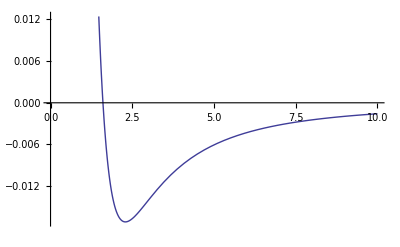

```mathematica
(* Worum geht es? Um das Maxima von T, was die Nullstelle der Ableitung ist. *)
Plot[Evaluate[(D[T[h,x,n],x] /.{L-> 1,n-> 1})],{x,0,10}]
```

```mathematica
(* Numerisch können Maxima von Subscript[T, H] leicht gefunden werden *)
```

```mathematica
Table[FindMaximum[L* T[h, x,n],{x,1}],{n,0,7}]
Table[FindMaximum[L*T[hA,x,n],{x,1}],{n,0,7}]
```

{{0.0238958,{x→2.05817}},{0.0701929,{x→1.60329}},{0.124212,{x→1.47529}},{0.182821,{x→1.40858}},{0.244657,{x→1.36369}},{0.308905,{x→1.32986}},{0.375024,{x→1.30288}},{0.442629,{x→1.28062}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.0243932,{x→1.96928}},{0.0738335,{x→1.46451}},{0.130736,{x→1.34302}},{0.191304,{x→1.29308}},{0.254375,{x→1.26483}},{0.319373,{x→1.24522}},{0.385925,{x→1.2299}},{0.453757,{x→1.21713}}}

```mathematica
(* Analytisch kann fuer h ein geschlossner Ausdruck gefunden werden: *)
Solve[L*D[T[h,x,n],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2^(1/(2+n)) (-4-3 n-n^2-(2+n) √(5+2 n+n^2))^(-1/(2+n))},{x→2^(1/(2+n)) (-4-3 n-n^2+(2+n) √(5+2 n+n^2))^(-1/(2+n))}}

```mathematica
(* Analytisch kann fuer Subscript[h, α] kein geschlossener Ausdruck mehr gefunden werden*)
Solve[L*D[T[hA,x,n],x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[L (-(1+n-((3+n) (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))/(2 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))))/(4 L π x^2)+(((3+n)^2 (1/x)^(1+((3+n) Log[(3+n)/2])/Log[2+n]) Log[(3+n)/2])/(2 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n])) Log[2+n])-((3+n)^2 (1/x)^(1+(2 (3+n) Log[(3+n)/2])/Log[2+n]) Log[(3+n)/2])/(4 (1+1/2 (1/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))^2 Log[2+n]))/(4 L π x))==0,x]

```mathematica
(* Sehr wohl aber bei Subscript[h, α] fuer feste n *)
Solve[(L*D[T[hA,x,n],x]/.{n-> 2})==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(1/2 (1-(25 Log[5/2])/Log[4]-(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(-Log[4]/(5 Log[5/2]))},{x→((-1)^(2/5)/((2/(1-(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(1/5)))^(-Log[4]/Log[5/2])},{x→(-(-1)^(3/5)/((2/(1-(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(1/5)))^(-Log[4]/Log[5/2])},{x→(2/(1-(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(Log[4]/(5 Log[5/2]))},{x→(-(-1)^(2/5)/((2/(-1+(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(1/5)))^(-Log[4]/Log[5/2])},{x→((-1)^(3/5)/((2/(-1+(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(1/5)))^(-Log[4]/Log[5/2])},{x→(-(-1)^(4/5)/((2/(-1+(25 Log[5/2])/Log[4]+(5 √(25 Log[5/2]^2-2 Log[5/2] Log[4]+Log[4]^2))/Log[4]))^(1/5)))^(-Log[4]/Log[5/2])}}